The curve y = x^2 from (1,1) to (2,4) is rotated about the x-axis. Find the area of the resulting surface.

```mathematica
Plot1 = Plot[x^2,{x,-3,3}];
Plot2 = ListPlot[Table[{i,i^2},{i,1,2}]];
```

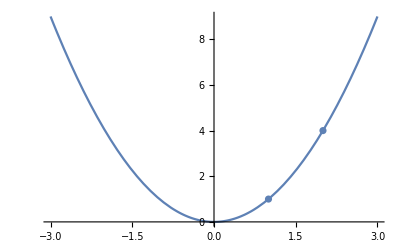

```mathematica
Show[Plot1,Plot2]
```

Solution:
	For rotation about x axis. The surface area becomes:

```mathematica
S=∫2Pi yⅆs
```

where we can use either
ds = √(1+(dy/dx)^2)dx     or     ds =√(1+(dx/dy)^2)dy

```mathematica
S1 = ∫_1^2 2Pi x^2 √(1+(2x)^2)ⅆx //N
```

49.4162

```mathematica
Clear[x]
```

```mathematica
Clear[y]
```

```mathematica
Solve[y == x^2, x, Reals]
```

{{x→ConditionalExpression[-√y, y>0]},{x→ConditionalExpression[√y, y>0]}}

```mathematica
D[√y,y]
```

1/(2 √y)

```mathematica
S1 = ∫_1^4 2Pi √y √(1+(1/(2 √y))^2)ⅆy //N
```

30.8465

```mathematica
S1 = ∫_1^2 2Pi x √(1+(2x)^2)ⅆx //N
```

30.8465